x y^2

{y^2,2 x y}

1/(1+r^2 s^2)

{√10,√5,√13,4 √2}

answer: {4,4} interpolation at r=0 {4,4}

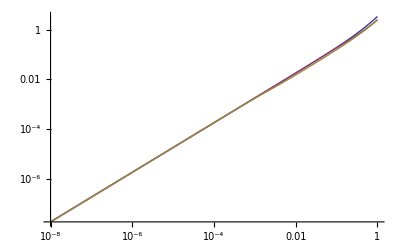

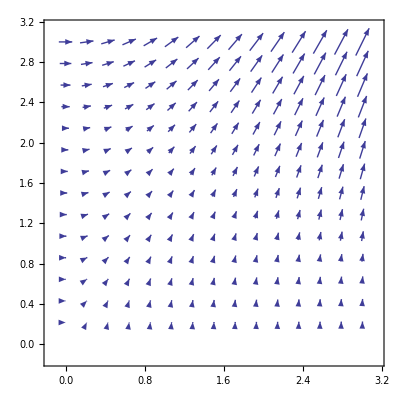

```mathematica
phi[x_,y_] = x*y*y

v[x_,y_] = {D[phi[x,y],x],D[phi[x,y],y]}


rbf[r_,s_] = 1/(1+(r*s)^2)
(* Plot[rbf[r,1],{r,0,10},PlotRange->All] *)

c = {1,2};

pts= {{-3,1}, {-1,2},{2,3},{-4,4}};
rs = Map[Norm,pts]
f[r_,s_] = Sum[v[c[[1]]+r pts[[i,1]],c[[2]]+r pts[[i,2]] ] rbf[r rs[[i]],s],{i,Length[rs]}]/Sum[rbf[r rs[[i]],s],{i,Length[rs]}];

Print["answer: ",vc = v[c[[1]],c[[2]]]," interpolation at r=0 ",f[0,1]]

error[r_,s_] = Norm[f[r,s]-vc]/Norm[vc];


LogLogPlot [{error[r,0.01],error[r,1],error[r,100]},{r,10^-8,1},PlotRange->All]

VectorPlot[v[x,y],{x,0,3},{y,0,3}]
```